！^2 ； 使用LaTex字符作为变量易引发BUG Null

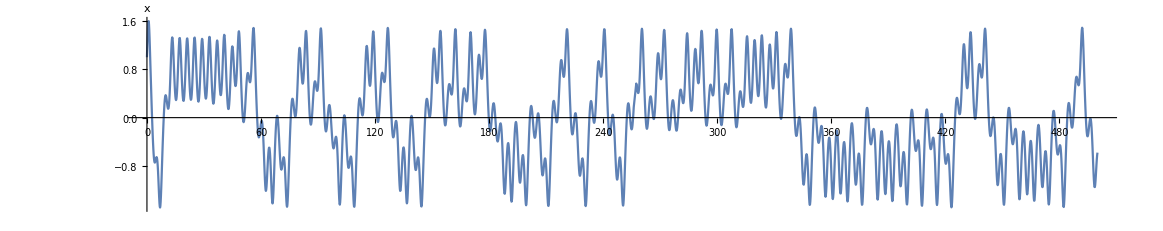

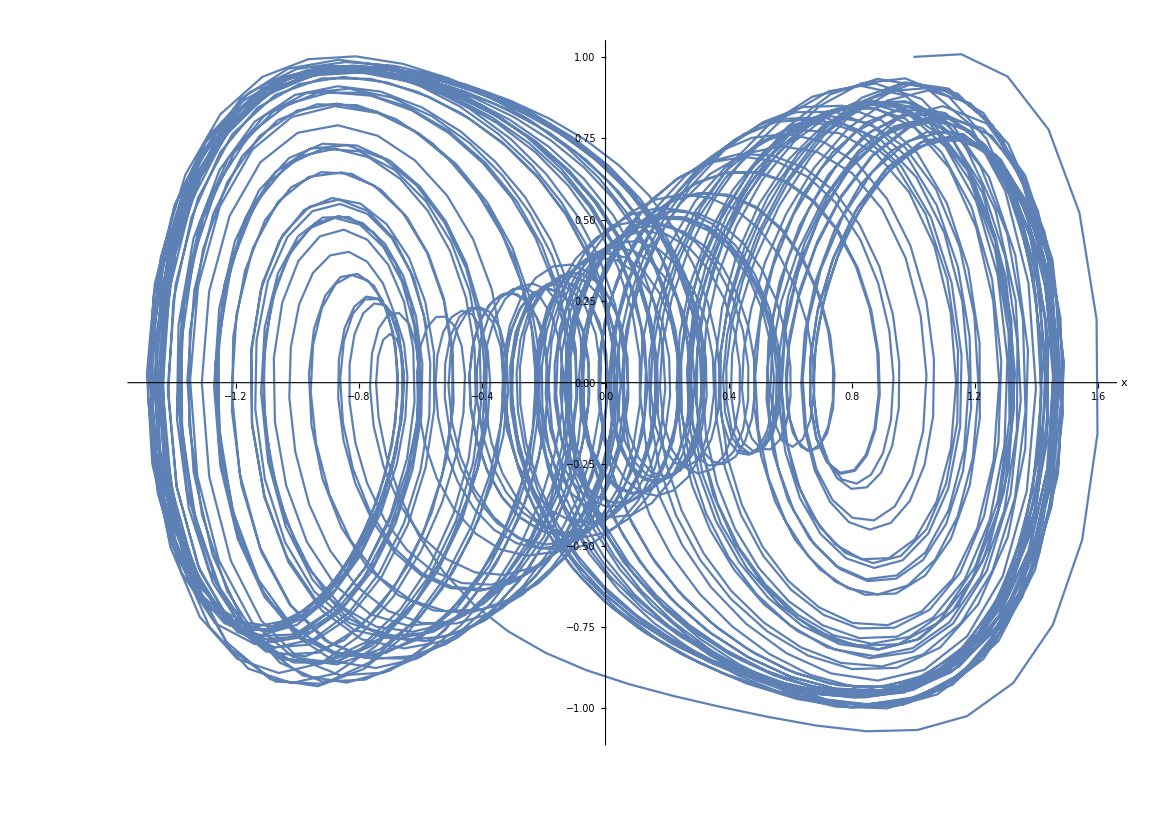

NDSolve::underdet: There are more dependent variables, {𝑥[𝜏],𝑥′[𝜏]}, than equations, so the system is underdetermined.

Plot::nonopt: Options expected (instead of Plot[duff[τ], {τ, 0, 500}, AxesLabel → {StyleBox[RowBox[{\"«\", \"173\", \"»\"}],StripOnInput->False,FontSize->Large], StyleBox[\"\\\"\<x\>\\\"\",StripOnInput->False,FontSize->Large]}, AxesStyle → Directive[22], AspectRatio → 0.2]) beyond position 2 in Plot[duff[:d70f], {:d70f, 0, 500}, Plot[duff[τ], {τ, 0, 500}, AxesLabel → {StyleBox[RowBox[{\"«\", \"173\", \"»\"}],StripOnInput->False,FontSize->Large], StyleBox[\"\\\"\<x\>\\\"\",StripOnInput->False,FontSize->Large]}, AxesStyle → Directive[22], AspectRatio → 0.2]]. An option must be a rule or a list of rules.

```mathematica
使用LaTex字符作为变量易引发BUG！！；

duff[t_]=NDSolve[{x''[t]+0.75*x'[t]-x[t]+x[t]^3==Cos[1.6*t],x[0]==1,x'[0]==1},x[t],{t,0,500}][[1,1,2]];

Plot[duff[t],{t,0,500},AxesLabel->{Style["",Large],Style["x",Larger]},AxesStyle->Directive[22],AspectRatio->0.2]
ParametricPlot[{duff[t],duff'[t]},{t,0,500},AxesLabel->{Style["x",Large],Style["",Larger]},AspectRatio->0.7,AxesStyle->Directive[22]]
```

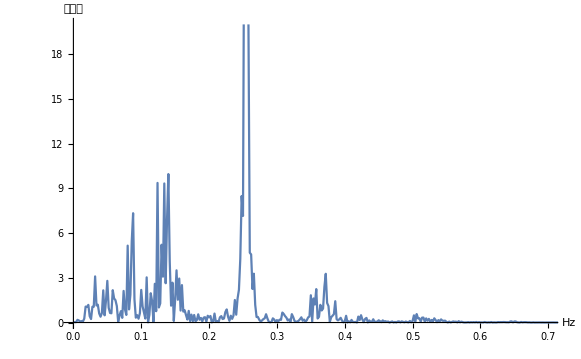

```mathematica
Tstep =0.1;
Totalpoints=5000;
Recordtime=Tstep*Totalpoints;
Recordsignal=Table[duff'[n*Tstep],{n,0,Totalpoints}];
transform=Abs[Fourier[Recordsignal]]^2;
frequencies=Table[n/Recordtime,{n,0,Totalpoints}];
data=Transpose[{frequencies,transform}];
ListPlot[data,Joined->True,PlotRange->{{0,0.7},{0,20}},AxesLabel->{Style["Hz",Larger],Style["谱强度",Larger]},AxesStyle->Directive[22]]
```

```mathematica
Manipulate[Module[{duff,x,t},duff[t_]=NDSolve[{x''[t]+0.78x'[t]-x[t]+x[t]^3==Cos[m*t],x[0]==0,x'[0]==0.8},x[t],{t,0,100}][[1,1,2]];
ParametricPlot[{duff[t],duff'[t]},{t,0,100},AspectRatio->1]],{{m,0.8},0.1,1.8}]
```

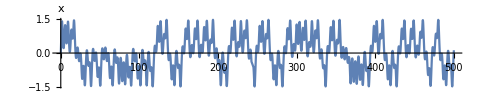

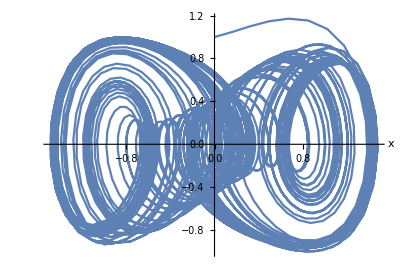

```mathematica
duff[t_]=NDSolve[{x''[t]+0.75*x'[t]-x[t]+x[t]^3==Cos[1.6*t],x[0]==0,x'[0]==1},x[t],{t,0,500}][[1,1,2]];

Plot[duff[t],{t,0,500},AxesLabel->{Style["",Large],Style["x",Larger]},AxesStyle->Directive[22],AspectRatio->0.2]
ParametricPlot[{duff[t],duff'[t]},{t,0,500},AxesLabel->{Style["x",Large],Style["",Larger]},AspectRatio->0.7,AxesStyle->Directive[22]]
```

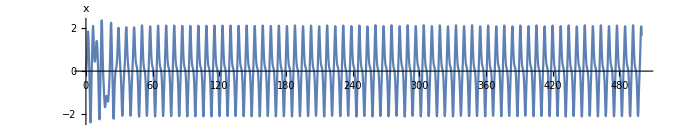

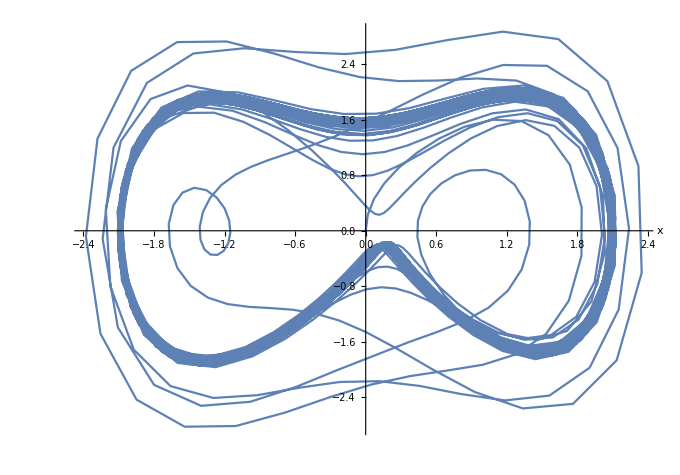

```mathematica
Clear["Global`*"]  (*Clear all variables*)
duff[t_]=NDSolve[{x''[t]+0.142*x'[t]-x[t]+x[t]^3==1.52*Cos[(1.31/1.51)*t],x[0]==0,x'[0]==0},x[t],{t,0,500}][[1,1,2]];

Plot[duff[t],{t,0,500},AxesLabel->{Style["",Large],Style["x",Larger]},AxesStyle->Directive[22],AspectRatio->0.2]
ParametricPlot[{duff[t],duff'[t]},{t,0,500},AxesLabel->{Style["x",Large],Style["",Larger]},AspectRatio->0.7,AxesStyle->Directive[22]]
```